## Day 3 morning — corrections

## Exercise 6: aggressivity under limited dispersal

### a. Individual fitness

```mathematica
Clear["Global`*"]
```

```mathematica
P[zi_,zj_] := V/2 + (V/2) (zi - zj) - Cc zi zj;
f[zi_,zj_] := f0 + δ P[zi, zj];
zbarF = (z1 + (n - 2) x)/(n - 1);
zbar1 = (zF + (n - 2) x)/(n - 1);
zbarR = (zF + z1 + (n - 3) x)/(n - 1);
fF = f[zF, zbarF];
f1 = f[z1, zbar1];
fR = f[x, zbarR];
fBar = (fF + f1 + (n - 2) fR)/n;
fResident = f[x, x];
w = s + (1 - s) (((1 - m) fF)/((1 - m) fBar + m fResident)+  (m fF)/fResident );
```

```mathematica
residentCheck = FullSimplify[w /. {zF -> x, z1 -> x } ];
residentCheck
```

1

The term s is adult survival. In the bracket, the first term is recruitment without dispersal and the second is recruitment after dispersal. At the resident state, all fecundities are equal and the three contributions add to one.

### b. Neutral relatedness

```mathematica
relatednessEquation = r2 == s^2 r2 + ( 2 s (1 - s) (1 - m) + (1 - s)^2 (1 - m)^2 ) (1/n + ((n - 1)/n) r2) 
r2Rule = Flatten@Solve[relatednessEquation , r2] 
r2Expr = r2 /. r2Rule ;
```

r2==r2 s^2+(1/n+((-1+n) r2)/n) ((1-m)^2 (1-s)^2+2 (1-m) (1-s) s)

{r2→((1-m)^2 (1-s)^2+2 (1-m) (1-s) s)/(n (1-s^2-((-1+n) ((1-m)^2 (1-s)^2+2 (1-m) (1-s) s))/n))}

```mathematica
specialCases = FullSimplify[{r2Expr/. m -> 0, r2Expr/. m -> 1, r2Expr/. s -> 0}];
specialCases
```

{1,0,-(-1+m)^2/(-1+(-2+m) m (-1+n))}

Relatedness rises with adult survival when 0 < m < 1, and falls with dispersal and patch size. For s < 1, patchmates eventually belong to the same lineage when m = 0. Complete dispersal gives r2 = 0.

### c. Evolution of aggressivity

The selection gradient is given by the inclusive fitness effect :

```mathematica
S = D[w,zF]+(n-1)r2Expr D[w,z1]   /. {zF -> x, z1 -> x} //Simplify ;
Sscaled = % * f[x,x]/(1-s)//Simplify
```

(m (8 Cc (-1+m) s x+n (2+m (-1+s)) (V-2 Cc x)) δ)/(2 (1+2 m (-1+n)+m^2 (-1+n) (-1+s)+s))

```mathematica
κ = 2 s (1-m)/(n (2-m)+s (2+(n-2) m)) ;
```

```mathematica
Solve[Sscaled ==k( (V/2-Cc x)+κ (-V/2-Cc x) ),k] //FullSimplify
```

{{k→(m (n (2+m (-1+s))-2 (-1+m) s) δ)/(1+m (-1+n) (2+m (-1+s))+s)}}

```mathematica
S ==δ (m (n (2+m (-1+s))-2 (-1+m) s))/(1+m (-1+n) (2+m (-1+s))+s) (1-s)/f[x,x]( (V/2-Cc x)+κ (-V/2-Cc x) )  //FullSimplify
```

True

```mathematica
Sreduced = (V/2-Cc x)+kappa (-V/2-Cc x) ;
```

```mathematica
sing = Flatten@Solve[Sreduced == 0, x] 
J = D[Sreduced, x] // Simplify
```

{x→(V-kappa V)/(2 Cc (1+kappa))}

-Cc (1+kappa)

Here kappa stands for κ. The singular phenotype is convergence stable because J < 0. Increasing κ lowers evolved aggressivity.

This is an interior singular phenotype when V (1 - κ) < 2 C (1 + κ). If the expression exceeds one, selection instead leads to the boundary x = 1.

The net social weight κ increases with adult survival and decreases with dispersal and patch size. Longer adult survival, less dispersal and smaller patches therefore favour lower aggressivity. When s = 0, κ = 0 even if relatedness is positive: local competition exactly cancels the relatedness effect.

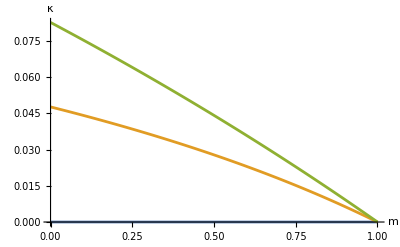

```mathematica
Plot[Evaluate[ κ /.n->10 /. s->{0,0.5,0.9}],{m,0,1},AxesLabel->{m,"κ"},PlotRange->All]
```

## Exercise 7: coordinated hunting under limited dispersal

```mathematica
Clear["Global`*"]
```

### a. Individual fitness

The patch life cycle and relatedness are unchanged from exercise 6. We only replace the payoff, then recompute fecundity and individual fitness.

```mathematica
P[zi_,zj_] := 1 - zi + 2 zi zj;
f[zi_,zj_] := f0 + δ P[zi, zj];
zbarF = (z1 + (n - 2) x)/(n - 1);
zbar1 = (zF + (n - 2) x)/(n - 1);
zbarR = (zF + z1 + (n - 3) x)/(n - 1);
fF = f[zF, zbarF];
f1 = f[z1, zbar1];
fR = f[x, zbarR];
fBar = (fF + f1 + (n - 2) fR)/n;
fResident = f[x, x];
w = s + (1 - s) (((1 - m) fF)/((1 - m) fBar + m fResident)+  (m fF)/fResident );
```

```mathematica
residentCheck = FullSimplify[w /. {zF -> x, z1 -> x}];
residentCheck
```

1

At the resident state, all individuals have the same fecundity and individual fitness equals one.

### b. Selection from individual fitness

As in exercise 6, start from the inclusive-fitness selection gradient.

```mathematica
r2Expr=((1-m)^2 (1-s)^2+2 (1-m) (1-s) s)/(n (1-s^2-((-1+n) ((1-m)^2 (1-s)^2+2 (1-m) (1-s) s))/n)) ;
```

```mathematica
S = (D[w, zF] + (n - 1) r2Expr D[w, z1]) /. {zF -> x, z1 -> x} // Simplify;
Sscaled = % * f[x, x] /(1 - s) // Simplify
```

(m (n (2+m (-1+s)) (-1+2 x)+2 s (-1+m+4 x-4 m x)) δ)/(1+2 m (-1+n)+m^2 (-1+n) (-1+s)+s)

```mathematica
κ = 2 s (1 - m)/(n (2 - m) + s (2 + (n - 2) m));
```

```mathematica
Solve[Sscaled == k ((-1 + 2 x) + κ (2 x)), k] // FullSimplify
```

{{k→(m (n (2+m (-1+s))-2 (-1+m) s) δ)/(1+m (-1+n) (2+m (-1+s))+s)}}

```mathematica
S == (m (n (2+m (-1+s))-2 (-1+m) s) δ)/(1+m (-1+n) (2+m (-1+s))+s)  (1 - s)/f[x, x]((-1 + 2 x) + κ (2 x)) // FullSimplify
```

True

The remaining factor is positive when δ > 0, 0 < m <= 1, s < 1 and resident fecundity is positive. The sign of selection is therefore the sign of (-1 + 2 x) + κ (2 x).

### c. The coordination threshold

```mathematica
Sreduced = (-1 + 2 x) + kappa (2 x);
```

```mathematica
sing = Flatten@Solve[Sreduced == 0, x]
J = D[Sreduced, x] // Simplify
```

{x→1/(2 (1+kappa))}

2 (1+kappa)

```mathematica
D[x/. sing, kappa] // Simplify
```

-1/(2 (1+kappa)^2)

Here kappa stands for κ. The singular phenotype is convergence unstable because J > 0. It is a threshold: populations below it evolve towards x = 0, whereas populations above it evolve towards x = 1.

Increasing adult survival, decreasing dispersal and decreasing patch size increase κ, so the threshold falls. The positive effect of hunting on a partner then receives more weight, allowing coordinated hunting to evolve from a lower initial x.

When s = 0 or m = 1, κ = 0 and the threshold is x = 1/2. The directional result assumes m > 0 and s < 1; at m = 0 or s = 1, the factor multiplying the reduced gradient is zero.

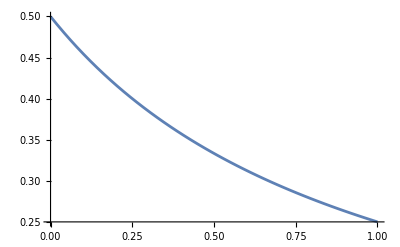

```mathematica
Plot[1/(2 (1+kappa)),{kappa,0,1}]
```